```mathematica
ClearAll["Global`*"]
```

If we want an additional mass-dependent mortality... we could use the predation window defined by Rohr to capture the additional mortality within a particular link-probability window... so that gives us pr(link) = f(M)... then predationmortality = ξf(M) for a particular predator size M_p

```mathematica
nsurv[q0_,α_,n0_] := n0*Exp[q0/α*(1-Exp[α*t])]
```

dn/dt = -d*n; d = -(1/n)*dn/dt

```mathematica
mortcohort=(-D[nsurv[q0,α,n0],t]*(1/(nsurv[q0,α,n0]))) (*1/time*)
```

ⅇ^(t α) q0

```mathematica
mortcorhortrate[q0_,α_] :=mortcohort
```

```mathematica
((1/texp)* Integrate[mortcorhortrate[q0,α],{t,0,texp}]);
avgmortrate[{q0_,α_,texp_}]:=((-1+ⅇ^(texp α)) q0)/(texp α)(*1/time*)
```

Here is the average mortality rate as a function of 
[q0: initial mortality rate (1/s); α: actuarial mortality rate (1/s); texp: expected lifespan (s)]

```mathematica
avgmortrate[{a0*M^b0, a1*M^b1, a2*M^b2}]
```

(a0 (-1+ⅇ^(a1 a2 M^(b1+b2))) M^(b0-b1-b2))/(a1 a2)

```mathematica
ϵLam = 0.95;
B0Prey=4.7*10^(-2);(*W g^−0.75*)
EmPrey=5774;(*J/gram*)
aPrey = B0Prey/EmPrey;
m0[M_]:=0.097*M^0.92;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/aPrey;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate *)
```

```mathematica
predratefull[Mp_,M_,ϵEprey_]:=(2.6153220589633594*^-24 M (1/(1-0.5549297692345301/Mp^0.01999999999999999))^4. ((1/(1.-0.5580754698496868/Mp^(1/50)))^2. (-144.9267622639406 Mp^0.21000000000000002+519.3805142626155 Mp^0.23-465.33178962560976 Mp^0.25)+(1/(1.-0.5580754698496868/Mp^(1/50)))^4. (-0.0006106484614702069 Mp^0.17000000000000004+0.004376816358795919 Mp^0.19000000000000003-0.01176404427874633 Mp^0.21000000000000002+0.014053110393730894 Mp^0.23-0.006295344963610381 Mp^0.25)+(1/(1.-0.5580754698496868/Mp^(1/50)))^3. (-0.4580132410244054 Mp^0.19000000000000003+2.4621037786220974 Mp^0.21000000000000002-4.4117756676982145 Mp^0.23+2.6351129348667315 Mp^0.25)+(1/(1.-0.5580754698496868/Mp^(1/50)))^1.0000000000000002 (-27175.36368464239 Mp^0.23+48694.78261060616 Mp^0.25)+23169.419606558215 Mp^0.17000000000000004+55355.52294339621 Mp^0.19000000000000003+148785.04593197524 Mp^0.21000000000000002+533207.6178587428 Mp^0.23-1.9904999661991596*^6 Mp^0.25-955439.9837755967 Mp^(1/4) Log[1/(78.483971592266-43.79997932202332/Mp^(1/50))]) ((-0.3774147476496817+(1.4319991297358558*^7)/((1/(1-0.5549297692345301/Mp^0.01999999999999999))^4.)) Mp^0.92+1.3266168798120597 (-3-221750.41668824226/((1/(1-0.5549297692345301/Mp^0.01999999999999999))^4.)-(2.320513787191087*^7 (-1+0.5549297692345301/Mp^0.01999999999999999))/((1/(1-0.5549297692345301/Mp^0.01999999999999999))^3.)-(1255.743545476256 (-1+0.5549297692345301/Mp^0.01999999999999999)^3)/((1/(1-0.5549297692345301/Mp^0.01999999999999999))^1.)+(3.79423204486181*^7 (-25+0.6835559388697282/Mp^0.05999999999999997+1.8476822926961325/Mp^0.03999999999999998+6.659157230814361/Mp^0.01999999999999999))/(1/(1-0.5549297692345301/Mp^0.01999999999999999))^4.+2.0506678166091845/Mp^0.05999999999999997-5.543046878088397/Mp^0.03999999999999998+6.659157230814361/Mp^0.01999999999999999) Mp-(6.040190731965005*^8 Mp Log[1/(78.483971592266-43.55309224430559/Mp^0.01999999999999999)])/((1/(1-0.5549297692345301/Mp^0.01999999999999999))^4.)))/(Mp^0.88 (-29.850746268656714 M+1. M^1.09263+M^1.19 (-0.1587762998305985-0.7557912252037328 ϵEprey)) Log[1/(78.483971592266-43.79997932202332/Mp^0.01999999999999999)])
```

A given prey has an optimal predator (just as we assume that a given predator has an optimal prey, given by OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M . When the optimal predator mass is inserted into the predation rate, and we plot across prey mass M, we get the following.

```mathematica
Manipulate[
LogLogPlot[{avgmortrate[{a0*M^b0, a1*M^b1, a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},λ[M],predratefull[OptPredMass[M],M,ϵEprey]},{M,1,1*10^8},Frame->True,FrameLabel->{"Herbivore Mass (g)","Rate s^-1"},PlotLegends->{"μ","λ","pred"}],{ϵEprey,-0.1,0.1}]
```

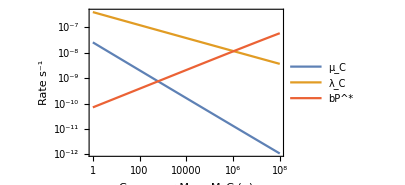

```mathematica
MortRateComparisonPlot = LogLogPlot[{avgmortrate[{a0*M^b0, a1*M^b1, a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},λ[M],predratefull[OptPredMass[M],M,0]},{M,1,1*10^8},Frame->True,FrameLabel->{"Consumer Mass M_C (g)","Rate s^-1"},PlotLegends->{"μ_C","λ_C","bP^*"},ImageSize->300,PlotStyle->Table[ColorData[97,i],{i,{1,2,4}}]]
```

```mathematica
Table[ColorData[97,i],{i,{1,2,4}}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.922526, 0.385626, 0.209179]}

```mathematica
Export[StringJoin[$HomeDirectory,"/DropBox/PostDoc/2021_TaranWebs/Figures/MortRateComparisonPlot.pdf"],MortRateComparisonPlot];
```

What is COOL is that there is a point where the predator mortality rate cross the reproduction rate... This happens at around M = 680000 grams (=10^2.84)... cow size. From Sinclair this is to the far right of the sigmoid... right at where there is no more predation... Could you say that at these sizes an herbivore population cannot support an ‘optimally’ sized carnivore population? So this escape from predation may in part be due to a prohibition on larger carnivore sizes that cannot be supported by larger herbivores????
-Graphics-
So a predator population requires a density given by the predator-Damuth law to maintain itself. A predator large enough to take down prey > 680 Kg (about) would need to extract so much biomass from the prey population that it cannot replenish itself, causing population collapse. So this would put a bounds on carnivores at OptPredMass[680000] =

```mathematica
OptPredMass[680000]
```

512582.

So this would be roughly the maximum sustainable carnivore mass! ^^^
It would be nice to solve this exactly... Below should work, but not analytically feasible.
Requires a numerical solution.

```mathematica
NSolve[predrate[OptPredMass[M]]==λ[M],M]
```

$Aborted

From Carbone et al. (Plos Biology) 2007
(though Megistotherium osteothlastes is estimated elsewhere at 500kg)
-Graphics-

Numerical Estimation of Maximum prey mass for a given predator population

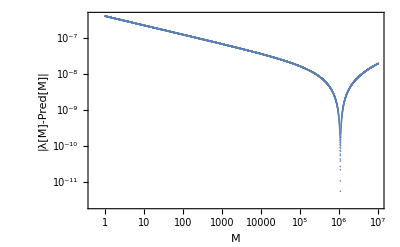

1.06414×10^6

802148.

```mathematica
RepMinusPred =Table[{10^i,Abs[λ[10^i]-predratefull[OptPredMass[10^i],10^i,0.0]]},{i,0,7,0.001}];
ListLogLogPlot[RepMinusPred,Frame->True,FrameLabel->{"M","|λ[M]-Pred[M]|"}]
MaxPreyMass=RepMinusPred[[Position[RepMinusPred,Min[RepMinusPred]][[1]][[1]]]][[1]]
MaxPredMass=OptPredMass[MaxPreyMass]
```

```mathematica
MaxPredDist=ParallelTable[
rv = RandomVariate[NormalDistribution[0,0.05]];
RepMinusPred =Table[{10^i,Abs[λ[10^i]-predratefull[OptPredMass[10^i],10^i,rv]]},{i,0,7,0.01}];
MaxPreyMass=RepMinusPred[[Position[RepMinusPred,Min[RepMinusPred]][[1]][[1]]]][[1]];
{OptPredMass[MaxPreyMass]},
{10000}];
```

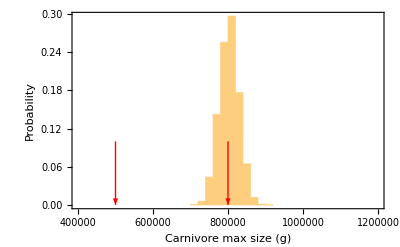

```mathematica
SH = 
Show[{
Histogram[Flatten[MaxPredDist,1],Automatic,"Probability",PlotRange->{{400000,1.2*^6},All},Frame->True,FrameLabel->{"Carnivore max size (g)","Probability"}],
Graphics[{Thick,Red,Arrow[{{800000,0.1},{800000,0.}}]}],
Graphics[{Thick,Red,Arrow[{{500000,0.1},{500000,0.}}]}](*,
Graphics[{Thick,ColorData[97,1],Dashed,Line[{{MaxPredMass,0},{MaxPredMass,0.4}}]}],
Graphics[{Thick,ColorData[97,1],Dashed,Line[{{MaxPreyMass,0},{MaxPreyMass,0.4}}]}]*)
}]
```

```mathematica
Export[StringJoin[$HomeDirectory,"/DropBox/PostDoc/2021_TaranWebs/Figures/MaxPredSizePlot.pdf"],SH];
```

```mathematica
lSH = Length[SH[[1]][[2]][[1]][[All,1]]];
adjdensity=Table[{SH[[1]][[2]][[1]][[All,1]][[i]],10^-8},{i,1,lSH}];
```

```mathematica
{{Log@MaxPreyMass,Log@(10^-14)},{Log@MaxPreyMass,Log@(1)}}
```

{{13.6774,-Log[100000000000000]},{13.6774,0}}

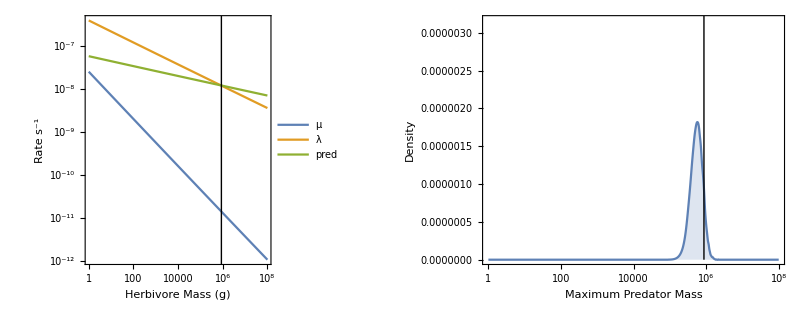

```mathematica
GraphicsGrid[{{
Show[{
LogLogPlot[{avgmortrate[{a0*M^b0, a1*M^b1, a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},λ[M],predratefull[OptPredMass[M],M,0]},{M,1,1*10^8},Frame->True,FrameLabel->{"Herbivore Mass (g)","Rate s^-1"},PlotLegends->Placed[{"μ","λ","pred"},{Left,Center}]],
Graphics[Line[{{Log@MaxPreyMass,Log@(10^-14)},{Log@MaxPreyMass,Log@(1)}}]]
}],
Show[{
 SmoothHistogram[Flatten[MaxPredDist,1],Filling->Bottom,Frame->True,ScalingFunctions->{"Log"},PlotRange->{{1,10^8},{0,10^-5.5}},FrameLabel->{"Maximum Predator Mass","Density"},PlotRange->All],
Graphics[Line[{{Log@MaxPreyMass,(10^-14)},{Log@MaxPreyMass,(10^-5)}}]]
(*Graphics[Line[{{Log@MaxPredMass,(10^-14)},{Log@MaxPredMass,(1)}}]]*)
}]
}},ImageSize->800]
```

```mathematica
Length[SH[[1]][[2]][[1]][[All,1]]]
```

1860

```mathematica
p = Exp[palpha + pbeta*Log[M/Mp] + pgamma*Log[M/Mp]^2];
avgmortratepred[dpred_,palpha_,pbeta_,pgamma_,M_,Mp_] :=dpred(( Exp[palpha + pbeta*Log[M/Mp] + pgamma*Log[M/Mp]^2])/(1+(Exp[palpha + pbeta*Log[M/Mp] + pgamma*Log[M/Mp]^2])));
```

```mathematica
Manipulate[
LogLogPlot[{avgmortrate[{a0*M^b0+avgmortratepred[predrate[10^Mpi],1.6332,0.2109,-0.3731,M,10^Mpi], a1*M^b1, a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},λ[M]},{M,1,1*10^8},Frame->True],{Mpi,1,5}]
```

```mathematica
Manipulate[
LogLogPlot[{avgmortrate[{a0*M^b0, a1*M^b1+avgmortratepred[predrate[10^Mpi],1.6332,0.2109,-0.3731,M,10^Mpi], a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},λ[M]},{M,1,1*10^8},Frame->True],{Mpi,1,5}]
```

```mathematica
Manipulate[
LogLogPlot[{avgmortrate[{a0*M^b0+predrate[10^Mpi], a1*M^b1, a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},λ[M]},{M,1,1*10^8},Frame->True],{Mpi,1,5}]
```

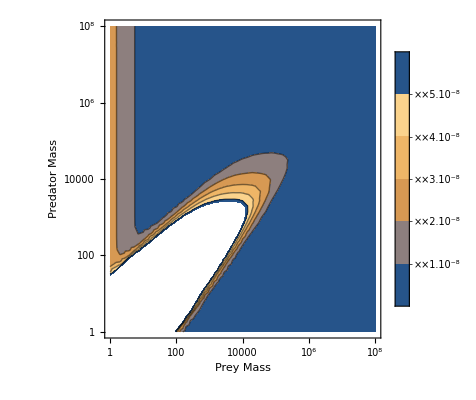

```mathematica
ContourPlot[{avgmortrate[{a0*M^b0+avgmortratepred[predrate[Mp],1.6332,0.2109,-0.3731,M,Mp], a1*M^b1, a2*M^b2}]/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30}},{M,1,1*10^8},{Mp,1,1*10^8},Frame->True,ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel->{"Prey Mass","Predator Mass"}]
```